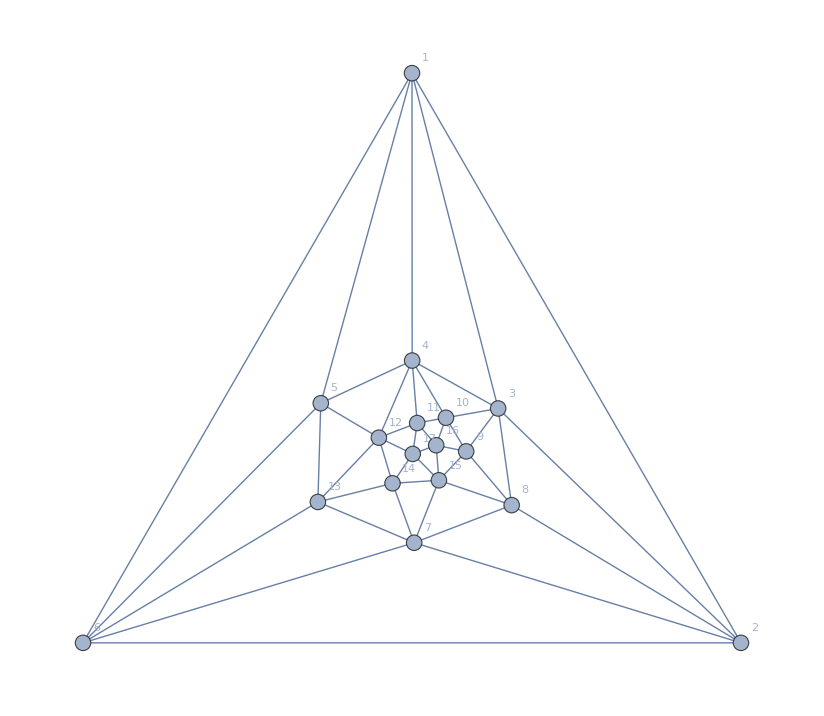

```mathematica
Graph[plantri[[8]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
EmbedGraph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
FakeEmbedGraph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
g=Graph[g,GraphHighlight->reference];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
g
]
```

```mathematica
atomKeys
```

{29524,29525,29527,29533,29537,29551,29560,29605,29608,29633,29767,29768,29797,29857,29888,30253,30262,30334,30496,30586,31711,31714,31738,31954,31984,32441,32684,36085,36086,36112,36166,36194,36817,36898,38281,38308,39014,49207,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
values2=Monitor[
Table[
With[
{g=FakeEmbedGraph5Plantri8[allGraphs,key]},
{key,allGraphs[key,"colofour"]}->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24,Factor[ChromaticPolynomial[g,x]],ChromaticPolynomial[g,x]}
]
,{key,Append[Sort[atomKeys],lambdaKey]}
]
,
key]
```

{{29524,v1x2x3x4x5}→{-Graphics-,628,(-3+x)^2 (-2+x)^3 (-1+x) x (-9539+26220 x-33813 x^2+26726 x^3-14180 x^4+5206 x^5-1316 x^6+220 x^7-22 x^8+x^9),-686808 x+4062732 x^2-11179006 x^3+19059385 x^4-22586469 x^5+19749882 x^6-13182082 x^7+6843891 x^8-2787401 x^9+890524 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16},{29525,v1x2x3x45}→{-Graphics-,192,(-3+x)^2 (-2+x)^2 (-1+x) x (-14996+39301 x-48094 x^2+36007 x^3-18099 x^4+6303 x^5-1514 x^6+241 x^7-23 x^8+x^9),539856 x-2854452 x^2+6958892 x^3-10430285 x^4+10785457 x^5-8164816 x^6+4675859 x^7-2060235 x^8+702159 x^9-184211 x^10+36611 x^11-5343 x^12+541 x^13-34 x^14+x^15},{29527,v1x2x35x4}→{-Graphics-,140,(-3+x)^2 (-2+x)^2 (-1+x) x (-26782+65709 x-74613 x^2+51634 x^3-24023 x^4+7786 x^5-1754 x^6+264 x^7-24 x^8+x^9),964152 x-4936596 x^2+11591986 x^3-16654199 x^4+16442078 x^5-11851394 x^6+6454081 x^7-2704798 x^8+878175 x^9-220055 x^10+41912 x^11-5883 x^12+575 x^13-35 x^14+x^15},{29533,v1x2x34x5}→{-Graphics-,260,(-3+x) (-2+x)^3 (-1+x) x (-21131+53859 x-63692 x^2+45900 x^3-22173 x^4+7420 x^5-1713 x^6+262 x^7-24 x^8+x^9),507144 x-2729524 x^2+6754714 x^3-10242331 x^4+10678371 x^5-8126153 x^6+4667353 x^7-2059291 x^8+702164 x^9-184224 x^10+36612 x^11-5343 x^12+541 x^13-34 x^14+x^15},{29537,v1x2x345}→{-Graphics-,68,(-3+x) (-2+x)^2 (-1+x) x (-30578+76205 x-87194 x^2+60298 x^3-27808 x^4+8866 x^5-1951 x^6+285 x^7-25 x^8+x^9),-366936 x+1770644 x^2-3883362 x^3+5162347 x^4-4667720 x^5+3045627 x^6-1480822 x^7+544728 x^8-151889 x^9+31741 x^10-4834 x^11+508 x^12-33 x^13+x^14},{29551,v1x25x3x4}→{-Graphics-,205,(-3+x)^2 (-2+x) (-1+x) x (64105-177131 x+229305 x^2-183802 x^3+101081 x^4-39776 x^5+11304 x^6-2282 x^7+312 x^8-26 x^9+x^10),1153890 x-5688453 x^2+12894644 x^3-17965075 x^4+17295865 x^5-12229261 x^6+6569608 x^7-2728967 x^8+881495 x^9-220326 x^10+41922 x^11-5883 x^12+575 x^13-35 x^14+x^15},{29560,v1x25x34}→{-Graphics-,93,(-3+x)^2 (-2+x) (-1+x) x (-42595+98056 x-104542 x^2+68178 x^3-30044 x^4+9266 x^5-1993 x^6+287 x^7-25 x^8+x^9),-766710 x+3426213 x^2-6941195 x^3+8531321 x^4-7156551 x^5+4354600 x^6-1986668 x^7+690181 x^8-182878 x^9+36519 x^10-5340 x^11+541 x^12-34 x^13+x^14},{29605,v1x24x3x5}→{-Graphics-,140,(-3+x)^2 (-2+x)^2 (-1+x) x (-26782+65709 x-74613 x^2+51634 x^3-24023 x^4+7786 x^5-1754 x^6+264 x^7-24 x^8+x^9),964152 x-4936596 x^2+11591986 x^3-16654199 x^4+16442078 x^5-11851394 x^6+6454081 x^7-2704798 x^8+878175 x^9-220055 x^10+41912 x^11-5883 x^12+575 x^13-35 x^14+x^15},{29608,v1x24x35}→{-Graphics-,37,(-3+x) (-2+x) (-1+x) x (218553-538873 x+617785 x^2-435653 x^3+209944 x^4-72351 x^5+18053 x^6-3215 x^7+390 x^8-29 x^9+x^10),-1311318 x+5637321 x^2-10945631 x^3+12861344 x^4-10297430 x^5+5975193 x^6-2599496 x^7+861923 x^8-218374 x^9+41807 x^10-5880 x^11+575 x^12-35 x^13+x^14},{29633,v1x245x3}→{-Graphics-,59,(-3+x)^2 (-2+x) (-1+x) x (-37105+89511 x-99091 x^2+66363 x^3-29715 x^4+9236 x^5-1992 x^6+287 x^7-25 x^8+x^9),-667890 x+3058293 x^2-6350612 x^3+7988847 x^4-6839370 x^5+4230990 x^6-1954153 x^7+684496 x^8-182250 x^9+36480 x^10-5339 x^11+541 x^12-34 x^13+x^14},{29767,v1x23x4x5}→{-Graphics-,192,(-3+x)^2 (-2+x)^2 (-1+x) x (-14996+39301 x-48094 x^2+36007 x^3-18099 x^4+6303 x^5-1514 x^6+241 x^7-23 x^8+x^9),539856 x-2854452 x^2+6958892 x^3-10430285 x^4+10785457 x^5-8164816 x^6+4675859 x^7-2060235 x^8+702159 x^9-184211 x^10+36611 x^11-5343 x^12+541 x^13-34 x^14+x^15},{29768,v1x23x45}→{-Graphics-,65,(-3+x)^2 (-2+x) (-1+x) x (-23371+58419 x-67840 x^2+48107 x^3-22916 x^4+7577 x^5-1732 x^6+263 x^7-24 x^8+x^9),-420678 x+1963011 x^2-4177220 x^3+5416176 x^4-4805163 x^5+3094192 x^6-1492046 x^7+546366 x^8-152026 x^9+31746 x^10-4834 x^11+508 x^12-33 x^13+x^14},{29797,v1x235x4}→{-Graphics-,59,(-3+x)^2 (-2+x) (-1+x) x (-37105+89511 x-99091 x^2+66363 x^3-29715 x^4+9236 x^5-1992 x^6+287 x^7-25 x^8+x^9),-667890 x+3058293 x^2-6350612 x^3+7988847 x^4-6839370 x^5+4230990 x^6-1954153 x^7+684496 x^8-182250 x^9+36480 x^10-5339 x^11+541 x^12-34 x^13+x^14},{29857,v1x234x5}→{-Graphics-,68,(-3+x) (-2+x)^2 (-1+x) x (-30578+76205 x-87194 x^2+60298 x^3-27808 x^4+8866 x^5-1951 x^6+285 x^7-25 x^8+x^9),-366936 x+1770644 x^2-3883362 x^3+5162347 x^4-4667720 x^5+3045627 x^6-1480822 x^7+544728 x^8-151889 x^9+31741 x^10-4834 x^11+508 x^12-33 x^13+x^14},{29888,v1x2345}→{-Graphics-,27,(-3+x) (-2+x) (-1+x) x (-42017+103199 x-115336 x^2+77273 x^3-34306 x^4+10487 x^5-2209 x^6+309 x^7-26 x^8+x^9),252102 x-1081381 x^2+2079307 x^3-2393545 x^4+1851054 x^5-1019262 x^6+411720 x^7-123381 x^8+27296 x^9-4355 x^10+476 x^11-32 x^12+x^13},{30253,v15x2x3x4}→{-Graphics-,240,(-3+x)^2 (-2+x)^2 (-1+x) x (-15308+39849 x-48482 x^2+36147 x^3-18125 x^4+6305 x^5-1514 x^6+241 x^7-23 x^8+x^9),551088 x-2904132 x^2+7055732 x^3-10540393 x^4+10866657 x^5-8205540 x^6+4689969 x^7-2063579 x^8+702679 x^9-184259 x^10+36613 x^11-5343 x^12+541 x^13-34 x^14+x^15},{30262,v15x2x34}→{-Graphics-,98,(-3+x) (-2+x)^2 (-1+x) x (-32783+79664 x-89368 x^2+60984 x^3-27917 x^4+8873 x^5-1951 x^6+285 x^7-25 x^8+x^9),-393396 x+1873892 x^2-4057017 x^3+5328648 x^4-4768115 x^5+3085392 x^6-1491187 x^7+546447 x^8-152054 x^9+31748 x^10-4834 x^11+508 x^12-33 x^13+x^14},{30334,v15x24x3}→{-Graphics-,58,(-3+x)^2 (-2+x) (-1+x) x (-39934+94018 x-102061 x^2+67404 x^3-29921 x^4+9258 x^5-1993 x^6+287 x^7-25 x^8+x^9),-718812 x+3249750 x^2-6661886 x^3+8279579 x^4-7013199 x^5+4300846 x^6-1973342 x^7+688068 x^8-182683 x^9+36511 x^10-5340 x^11+541 x^12-34 x^13+x^14},{30496,v15x23x4}→{-Graphics-,73,(-3+x)^2 (-2+x) (-1+x) x (-23771+59101 x-68305 x^2+48267 x^3-22944 x^4+7579 x^5-1732 x^6+263 x^7-24 x^8+x^9),-427878 x+1990887 x^2-4223788 x^3+5460569 x^4-4831930 x^5+3104827 x^6-1494841 x^7+546836 x^8-152072 x^9+31748 x^10-4834 x^11+508 x^12-33 x^13+x^14},{30586,v15x234}→{-Graphics-,27,(-3+x) (-2+x) (-1+x) x (-45677+109186 x-119340 x^2+78669 x^3-34572 x^4+10513 x^5-2210 x^6+309 x^7-26 x^8+x^9),274062 x-1157563 x^2+2191148 x^3-2485547 x^4+1898017 x^5-1034724 x^6+415004 x^7-123814 x^8+27328 x^9-4356 x^10+476 x^11-32 x^12+x^13},{31711,v14x2x3x5}→{-Graphics-,164,(-3+x)^3 (-2+x)^3 (-1+x) x (-3083+5841 x-5009 x^2+2524 x^3-805 x^4+162 x^5-19 x^6+x^7),665928 x-3592404 x^2+8882874 x^3-13406035 x^4+13849723 x^5-10395373 x^6+5862416 x^7-2529234 x^8+840391 x^9-214304 x^10+41325 x^11-5847 x^12+574 x^13-35 x^14+x^15},{31714,v14x2x35}→{-Graphics-,44,(-3+x) (-2+x)^2 (-1+x) x (-78362+172208 x-174237 x^2+107001 x^3-44065 x^4+12627 x^5-2515 x^6+335 x^7-27 x^8+x^9),-940344 x+4260632 x^2-8714994 x^3+10750328 x^4-8988285 x^5+5412471 x^6-2427476 x^7+824382 x^8-212630 x^9+41220 x^10-5844 x^11+574 x^12-35 x^13+x^14},{31738,v14x25x3}→{-Graphics-,55,(-3+x)^2 (-2+x) (-1+x) x (-61021+134477 x-137994 x^2+86752 x^3-36814 x^4+10912 x^5-2252 x^6+311 x^7-26 x^8+x^9),-1098378 x+4800405 x^2-9498104 x^3+11392324 x^4-9319120 x^5+5524393 x^6-2452472 x^7+827952 x^8-212927 x^9+41231 x^10-5844 x^11+574 x^12-35 x^13+x^14},{31954,v14x23x5}→{-Graphics-,56,(-3+x)^3 (-2+x)^2 (-1+x) x (-4584+8229 x-6649 x^2+3152 x^3-947 x^4+180 x^5-20 x^6+x^7),-495072 x+2373948 x^2-5158296 x^3+6770307 x^4-6021909 x^5+3851050 x^6-1828855 x^7+655109 x^8-177441 x^9+35957 x^10-5305 x^11+540 x^12-34 x^13+x^14},{31984,v14x235}→{-Graphics-,20,(-3+x) (-2+x) (-1+x) x (-104240+226089 x-224050 x^2+133823 x^3-53302 x^4+14717 x^5-2819 x^6+361 x^7-28 x^8+x^9),625440 x-2503174 x^2+4456719 x^3-4728262 x^4+3362254 x^5-1701612 x^6+632436 x^7-174779 x^8+35770 x^9-5299 x^10+540 x^11-34 x^12+x^13},{32441,v145x2x3}→{-Graphics-,82,(-3+x)^3 (-2+x)^2 (-1+x) x (-3083+5841 x-5009 x^2+2524 x^3-805 x^4+162 x^5-19 x^6+x^7),-332964 x+1629720 x^2-3626577 x^3+4889729 x^4-4479997 x^5+2957688 x^6-1452364 x^7+538435 x^8-150978 x^9+31663 x^10-4831 x^11+508 x^12-33 x^13+x^14},{32684,v145x23}→{-Graphics-,28,(-3+x)^3 (-2+x) (-1+x) x (-4584+8229 x-6649 x^2+3152 x^3-947 x^4+180 x^5-20 x^6+x^7),247536 x-1063206 x^2+2047545 x^3-2361381 x^4+1830264 x^5-1010393 x^6+409231 x^7-122939 x^8+27251 x^9-4353 x^10+476 x^11-32 x^12+x^13},{36085,v13x2x4x5}→{-Graphics-,164,(-3+x)^3 (-2+x)^3 (-1+x) x (-3083+5841 x-5009 x^2+2524 x^3-805 x^4+162 x^5-19 x^6+x^7),665928 x-3592404 x^2+8882874 x^3-13406035 x^4+13849723 x^5-10395373 x^6+5862416 x^7-2529234 x^8+840391 x^9-214304 x^10+41325 x^11-5847 x^12+574 x^13-35 x^14+x^15},{36086,v13x2x45}→{-Graphics-,56,(-3+x)^3 (-2+x)^2 (-1+x) x (-4584+8229 x-6649 x^2+3152 x^3-947 x^4+180 x^5-20 x^6+x^7),-495072 x+2373948 x^2-5158296 x^3+6770307 x^4-6021909 x^5+3851050 x^6-1828855 x^7+655109 x^8-177441 x^9+35957 x^10-5305 x^11+540 x^12-34 x^13+x^14},{36112,v13x25x4}→{-Graphics-,55,(-3+x)^2 (-2+x) (-1+x) x (-61021+134477 x-137994 x^2+86752 x^3-36814 x^4+10912 x^5-2252 x^6+311 x^7-26 x^8+x^9),-1098378 x+4800405 x^2-9498104 x^3+11392324 x^4-9319120 x^5+5524393 x^6-2452472 x^7+827952 x^8-212927 x^9+41231 x^10-5844 x^11+574 x^12-35 x^13+x^14},{36166,v13x24x5}→{-Graphics-,44,(-3+x) (-2+x)^2 (-1+x) x (-78362+172208 x-174237 x^2+107001 x^3-44065 x^4+12627 x^5-2515 x^6+335 x^7-27 x^8+x^9),-940344 x+4260632 x^2-8714994 x^3+10750328 x^4-8988285 x^5+5412471 x^6-2427476 x^7+824382 x^8-212630 x^9+41220 x^10-5844 x^11+574 x^12-35 x^13+x^14},{36194,v13x245}→{-Graphics-,20,(-3+x) (-2+x) (-1+x) x (-104240+226089 x-224050 x^2+133823 x^3-53302 x^4+14717 x^5-2819 x^6+361 x^7-28 x^8+x^9),625440 x-2503174 x^2+4456719 x^3-4728262 x^4+3362254 x^5-1701612 x^6+632436 x^7-174779 x^8+35770 x^9-5299 x^10+540 x^11-34 x^12+x^13},{36817,v135x2x4}→{-Graphics-,68,(-3+x)^3 (-2+x)^2 (-1+x) x (-4354+7993 x-6560 x^2+3137 x^3-946 x^4+180 x^5-20 x^6+x^7),-470232 x+2273940 x^2-4983210 x^3+6593779 x^4-5907930 x^5+3801639 x^6-1814244 x^7+652189 x^8-177062 x^9+35928 x^10-5304 x^11+540 x^12-34 x^13+x^14},{36898,v135x24}→{-Graphics-,21,(-3+x) (-2+x) (-1+x) x (-104927+226861 x-224372 x^2+133882 x^3-53306 x^4+14717 x^5-2819 x^6+361 x^7-28 x^8+x^9),629562 x-2515363 x^2+4471265 x^3-4737477 x^4+3365631 x^5-1702332 x^6+632519 x^7-174783 x^8+35770 x^9-5299 x^10+540 x^11-34 x^12+x^13},{38281,v134x2x5}→{-Graphics-,64,(-3+x)^2 (-2+x)^3 (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),-349344 x+1765560 x^2-4042148 x^3+5575642 x^4-5189481 x^5+3453256 x^6-1695456 x^7+623643 x^8-172315 x^9+35407 x^10-5270 x^11+539 x^12-34 x^13+x^14},{38308,v134x25}→{-Graphics-,25,(-3+x) (-2+x) (-1+x) x (-90819+201395 x-204719 x^2+125468 x^3-51148 x^4+14386 x^5-2791 x^6+360 x^7-28 x^8+x^9),544914 x-2207379 x^2+3988573 x^3-4303906 x^4+3116745 x^5-1606471 x^6+607348 x^7-170325 x^8+35260 x^9-5265 x^10+539 x^11-34 x^12+x^13},{39014,v1345x2}→{-Graphics-,32,(-3+x)^2 (-2+x)^2 (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),174672 x-795444 x^2+1623352 x^3-1976145 x^4+1606668 x^5-923294 x^6+386081 x^7-118781 x^8+26767 x^9-4320 x^10+475 x^11-32 x^12+x^13},{49207,v12x3x4x5}→{-Graphics-,240,(-3+x)^2 (-2+x)^2 (-1+x) x (-15308+39849 x-48482 x^2+36147 x^3-18125 x^4+6305 x^5-1514 x^6+241 x^7-23 x^8+x^9),551088 x-2904132 x^2+7055732 x^3-10540393 x^4+10866657 x^5-8205540 x^6+4689969 x^7-2063579 x^8+702679 x^9-184259 x^10+36613 x^11-5343 x^12+541 x^13-34 x^14+x^15},{49208,v12x3x45}→{-Graphics-,73,(-3+x)^2 (-2+x) (-1+x) x (-23771+59101 x-68305 x^2+48267 x^3-22944 x^4+7579 x^5-1732 x^6+263 x^7-24 x^8+x^9),-427878 x+1990887 x^2-4223788 x^3+5460569 x^4-4831930 x^5+3104827 x^6-1494841 x^7+546836 x^8-152072 x^9+31748 x^10-4834 x^11+508 x^12-33 x^13+x^14},{49210,v12x35x4}→{-Graphics-,58,(-3+x)^2 (-2+x) (-1+x) x (-39934+94018 x-102061 x^2+67404 x^3-29921 x^4+9258 x^5-1993 x^6+287 x^7-25 x^8+x^9),-718812 x+3249750 x^2-6661886 x^3+8279579 x^4-7013199 x^5+4300846 x^6-1973342 x^7+688068 x^8-182683 x^9+36511 x^10-5340 x^11+541 x^12-34 x^13+x^14},{49216,v12x34x5}→{-Graphics-,98,(-3+x) (-2+x)^2 (-1+x) x (-32783+79664 x-89368 x^2+60984 x^3-27917 x^4+8873 x^5-1951 x^6+285 x^7-25 x^8+x^9),-393396 x+1873892 x^2-4057017 x^3+5328648 x^4-4768115 x^5+3085392 x^6-1491187 x^7+546447 x^8-152054 x^9+31748 x^10-4834 x^11+508 x^12-33 x^13+x^14},{49220,v12x345}→{-Graphics-,27,(-3+x) (-2+x) (-1+x) x (-45677+109186 x-119340 x^2+78669 x^3-34572 x^4+10513 x^5-2210 x^6+309 x^7-26 x^8+x^9),274062 x-1157563 x^2+2191148 x^3-2485547 x^4+1898017 x^5-1034724 x^6+415004 x^7-123814 x^8+27328 x^9-4356 x^10+476 x^11-32 x^12+x^13},{49963,v125x3x4}→{-Graphics-,99,(-3+x)^2 (-2+x) (-1+x) x (-23741+59196 x-68469 x^2+48358 x^3-22966 x^4+7581 x^5-1732 x^6+263 x^7-24 x^8+x^9),-427338 x+1991427 x^2-4229575 x^3+5471088 x^4-4841456 x^5+3109931 x^6-1496540 x^7+547183 x^8-152112 x^9+31750 x^10-4834 x^11+508 x^12-33 x^13+x^14},{49972,v125x34}→{-Graphics-,42,(-3+x) (-2+x) (-1+x) x (-47882+112645 x-121514 x^2+79355 x^3-34681 x^4+10520 x^5-2210 x^6+309 x^7-26 x^8+x^9),287292 x-1202572 x^2+2255471 x^3-2536536 x^4+1922720 x^5-1042255 x^6+416421 x^7-123965 x^8+27335 x^9-4356 x^10+476 x^11-32 x^12+x^13},{51475,v124x3x5}→{-Graphics-,68,(-3+x)^3 (-2+x)^2 (-1+x) x (-4354+7993 x-6560 x^2+3137 x^3-946 x^4+180 x^5-20 x^6+x^7),-470232 x+2273940 x^2-4983210 x^3+6593779 x^4-5907930 x^5+3801639 x^6-1814244 x^7+652189 x^8-177062 x^9+35928 x^10-5304 x^11+540 x^12-34 x^13+x^14},{51478,v124x35}→{-Graphics-,21,(-3+x) (-2+x) (-1+x) x (-104927+226861 x-224372 x^2+133882 x^3-53306 x^4+14717 x^5-2819 x^6+361 x^7-28 x^8+x^9),629562 x-2515363 x^2+4471265 x^3-4737477 x^4+3365631 x^5-1702332 x^6+632519 x^7-174783 x^8+35770 x^9-5299 x^10+540 x^11-34 x^12+x^13},{52232,v1245x3}→{-Graphics-,34,(-3+x)^3 (-2+x) (-1+x) x (-4354+7993 x-6560 x^2+3137 x^3-946 x^4+180 x^5-20 x^6+x^7),235116 x-1019412 x^2+1981899 x^3-2305940 x^4+1800995 x^5-1000322 x^6+406961 x^7-122614 x^8+27224 x^9-4352 x^10+476 x^11-32 x^12+x^13},{56011,v123x4x5}→{-Graphics-,82,(-3+x)^3 (-2+x)^2 (-1+x) x (-3083+5841 x-5009 x^2+2524 x^3-805 x^4+162 x^5-19 x^6+x^7),-332964 x+1629720 x^2-3626577 x^3+4889729 x^4-4479997 x^5+2957688 x^6-1452364 x^7+538435 x^8-150978 x^9+31663 x^10-4831 x^11+508 x^12-33 x^13+x^14},{56012,v123x45}→{-Graphics-,28,(-3+x)^3 (-2+x) (-1+x) x (-4584+8229 x-6649 x^2+3152 x^3-947 x^4+180 x^5-20 x^6+x^7),247536 x-1063206 x^2+2047545 x^3-2361381 x^4+1830264 x^5-1010393 x^6+409231 x^7-122939 x^8+27251 x^9-4353 x^10+476 x^11-32 x^12+x^13},{56770,v1235x4}→{-Graphics-,34,(-3+x)^3 (-2+x) (-1+x) x (-4354+7993 x-6560 x^2+3137 x^3-946 x^4+180 x^5-20 x^6+x^7),235116 x-1019412 x^2+1981899 x^3-2305940 x^4+1800995 x^5-1000322 x^6+406961 x^7-122614 x^8+27224 x^9-4352 x^10+476 x^11-32 x^12+x^13},{58288,v1234x5}→{-Graphics-,32,(-3+x)^2 (-2+x)^2 (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),174672 x-795444 x^2+1623352 x^3-1976145 x^4+1606668 x^5-923294 x^6+386081 x^7-118781 x^8+26767 x^9-4320 x^10+475 x^11-32 x^12+x^13},{59048,v12345}→{-Graphics-,16,(-3+x)^2 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),-87336 x+354054 x^2-634649 x^3+670748 x^4-467960 x^5+227667 x^6-79207 x^7+19787 x^8-3490 x^9+415 x^10-30 x^11+x^12},{20665,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5}→{-Graphics-,628,(-3+x)^2 (-2+x)^3 (-1+x) x (-9539+26220 x-33813 x^2+26726 x^3-14180 x^4+5206 x^5-1316 x^6+220 x^7-22 x^8+x^9),-686808 x+4062732 x^2-11179006 x^3+19059385 x^4-22586469 x^5+19749882 x^6-13182082 x^7+6843891 x^8-2787401 x^9+890524 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16}}

```mathematica
values=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
{key,allGraphs[key,"colofour"]}->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24,Factor[ChromaticPolynomial[g,x]],ChromaticPolynomial[g,x]}
]
,{key,Append[Sort[atomKeys],lambdaKey]}
]
,
key];
```

## Here we have the results

To my surprise we see that only one triangle has a zero embedded colofour.

```mathematica
TableForm[Select[Sort[values,#1[[1,1]]<#2[[1,1]]&],MemberQ[{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key},#[[1,1]]]&]]
```

{29527,v1x2x35x4}→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11)}
{29551,v1x25x3x4}→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-1746193+4433963 x-5258709 x^2+3861711 x^3-1956730 x^4+719298 x^5-195702 x^6+39350 x^7-5717 x^8+570 x^9-35 x^10+x^11)}
{29605,v1x24x3x5}→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11)}
{29608,v1x24x35}→{-Graphics-,0,(-4+x) (-3+x) (-2+x) (-1+x) x (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9)}
{31711,v14x2x3x5}→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11)}
{31714,v14x2x35}→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10)}
{31738,v14x25x3}→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10)}
{36085,v13x2x4x5}→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11)}
{36112,v13x25x4}→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10)}
{36166,v13x24x5}→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10)}

## Verify the result

```mathematica
amigo1Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,1<->3]&&
EdgeQ[g,1<->4]
]&]]
```

29413

```mathematica
amigo2Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,2<->5]&&
EdgeQ[g,2<->4]
]&]]
```

20773

```mathematica
amigo3Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,3<->5]&&
EdgeQ[g,3<->1]
]&]]
```

27229

```mathematica
amigo4Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,4<->1]&&
EdgeQ[g,4<->2]
]&]]
```

22933

```mathematica
amigo5Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,5<->3]&&
EdgeQ[g,5<->2]
]&]]
```

20695

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29413],4]/24
```

23

```mathematica
allGraphs[29413,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,23}

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,20773],4]/24
```

27

```mathematica
allGraphs[20773,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,27}

## Trying to find a link between the alfa beta an dthe quadrilaterals

```mathematica
valuesalfa=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}
]
,
key]
```

{v13x24x5→{-Graphics-,3},v14x25x3→{-Graphics-,8},v1x24x35→{-Graphics-,0},v13x25x4→{-Graphics-,8},v14x2x35→{-Graphics-,3}}

```mathematica
Total[Map[#[[2,2]]&,valuesalfa]]
```

22

```mathematica
valuesquad=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{29605,36085,29551,31711,29527}}
]
,
key]
```

{v1x24x3x5→{-Graphics-,6},v13x2x4x5→{-Graphics-,9},v1x25x3x4→{-Graphics-,11},v14x2x3x5→{-Graphics-,9},v1x2x35x4→{-Graphics-,6}}

```mathematica
Total[Map[#[[2,2]]&,valuesquad]]
```

41

```mathematica
IsomorphicGraphQ[DualGraph[Faces[GraphData["PetersenGraph"]]],CompleteGraph[7]]
```

True

```mathematica
GraphData["PetersenGraph","CochromaticGraphs"]
```

{}

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
GraphData["PetersenGraph","ChromaticPolynomial"][x]
```

(-2+x) (-1+x) x (-352+775 x-814 x^2+529 x^3-230 x^4+67 x^5-12 x^6+x^7)

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
FlowPolynomial[CompleteGraph[7],x]//Factor
```

(-1+x) (7575-34365 x+81625 x^2-133100 x^3+163756 x^4-158405 x^5+122785 x^6-76785 x^7+38655 x^8-15497 x^9+4845 x^10-1140 x^11+190 x^12-20 x^13+x^14)

```mathematica
FlowPolynomial[DualGraph[Faces[CompleteGraph[4]]],x]//Factor
```

(-3+x) (-2+x) (-1+x)

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//Factor
```

(-3+x) (-2+x) (-1+x) x

```mathematica
FlowPolynomial[DualGraph[Faces[allGraphs[29413,"graph"]]]][x]//Factor
```

(-2+x) (-1+x)

```mathematica
ChromaticPolynomial[allGraphs[29413,"graph"],x]//Factor
```

(-2+x)^3 (-1+x) x

```mathematica
allGraphs[29413,"graph"]
```

-Graphics-

```mathematica
Faces[allGraphs[29413,"graph"]]
```

{{1<->2,1<->3,2<->3},{1<->3,1<->4,3<->4},{1<->4,1<->5,4<->5}}

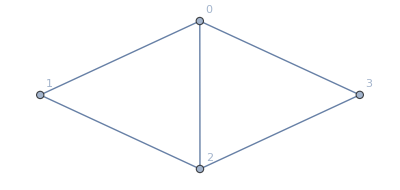

```mathematica
Graph[DualGraph[Faces[allGraphs[29413,"graph"]]],VertexLabels->"Name"]
```

```mathematica
Reduce[x-a>b,x]
```

(a|b)∈Reals&&x>a+b